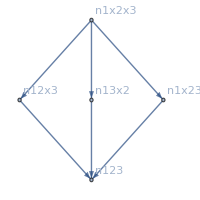
{-Graphics-→-Graphics-0,-Graphics-→-Graphics-1,-Graphics-→-Graphics-2,-Graphics-→-Graphics-3,-Graphics-→-Graphics-4,-Graphics-→-Graphics-6,-Graphics-→-Graphics-9,-Graphics-→-Graphics-10,-Graphics-→-Graphics-12,-Graphics-→-Graphics-13,-Graphics-→-Graphics-14,-Graphics-→-Graphics-16,-Graphics-→-Graphics-18,-Graphics-→-Graphics-22,-Graphics-→-Graphics-26}

```mathematica
With[{full=MobiusGraph4[13,allGraphs3]},
Table[
allGraphs3[k,"graph"]->
Labeled[
With[{sub2=MobiusGraph4[k,allGraphs3]},
Graph[EdgeList[full],GraphHighlight->Join[EdgeList[sub2],VertexList[sub2]],ImageSize->200, VertexLabels->"Name"]
],
{k},{Top}
]
,{k,Sort[Keys[allGraphs3]]}]
]
```

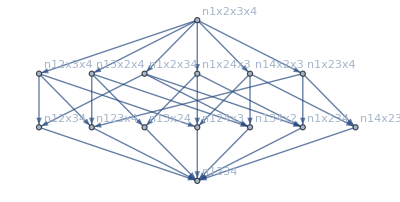
-Graphics-→-Graphics-13
-Graphics-→-Graphics-40
-Graphics-→-Graphics-94
-Graphics-→-Graphics-109
-Graphics-→-Graphics-112
-Graphics-→-Graphics-118
-Graphics-→-Graphics-121
-Graphics-→-Graphics-256
-Graphics-→-Graphics-273
-Graphics-→-Graphics-274
-Graphics-→-Graphics-282
-Graphics-→-Graphics-283
-Graphics-→-Graphics-333
-Graphics-→-Graphics-334
-Graphics-→-Graphics-336
-Graphics-→-Graphics-337
-Graphics-→-Graphics-352
-Graphics-→-Graphics-354
-Graphics-→-Graphics-355
-Graphics-→-Graphics-360
-Graphics-→-Graphics-361
-Graphics-→-Graphics-363
-Graphics-→-Graphics-364
-Graphics-→-Graphics-365
-Graphics-→-Graphics-367
-Graphics-→-Graphics-373
-Graphics-→-Graphics-391
-Graphics-→-Graphics-445
-Graphics-→-Graphics-607

```mathematica
TableForm[
With[{full=MobiusGraph4[K4Key,allGraphs4]},
Table[
allGraphs4[k,"graph"]->
Labeled[
With[{sub2=MobiusGraph4[k,allGraphs4]},
Graph[EdgeList[full],GraphHighlight->Join[EdgeList[sub2],VertexList[sub2]],ImageSize->400, VertexLabels->"Name"]
],
{k},{Top}
]
,{k,Select[Sort[Keys[allGraphs4]],ChromaticPolynomial[allGraphs4[#,"graph"],2]==0&]}]
]
]
```

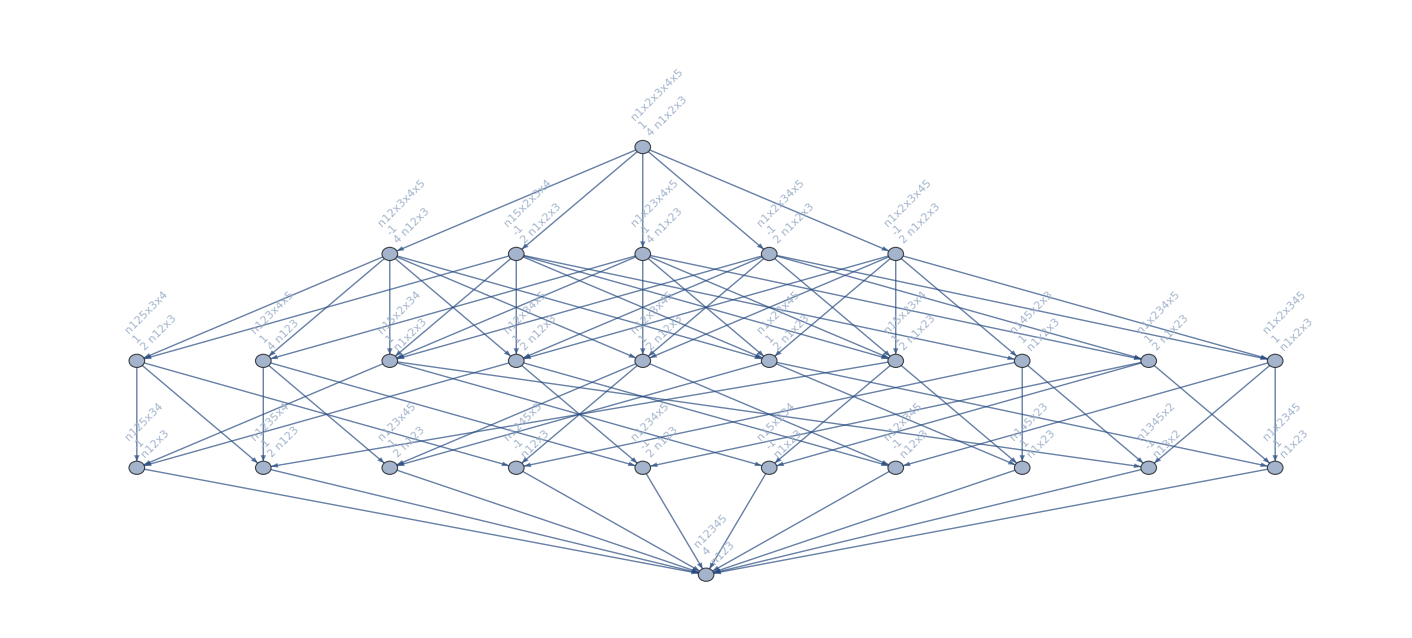

```mathematica
MobiusGraph4[lambdaKey,allGraphs5]
```

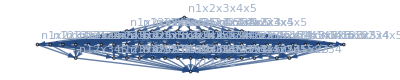
{-Graphics-→-Graphics-20665,-Graphics-→-Graphics-36166}

```mathematica
With[{full=MobiusGraph4[k5Key,allGraphs5]},
Table[
allGraphs5[k,"graph"]->
Labeled[
With[{sub2=MobiusGraph4[k,allGraphs5]},
Graph[EdgeList[full],GraphHighlight->Join[EdgeList[sub2],VertexList[sub2]],ImageSize->400, VertexLabels->"Name",GraphLayout->"LayeredDigraphEmbedding"]
],
{k},{Top}
]
,{k,{lambdaKey,alfa1Key}}]
]
```